PAPERS
- Zwickl, P., Reichl, P., Skorin-Kapov, L., Dobrijevic, O., & Sackl, A. (2015). On the Approximation of ISP and User Utilities from Quality of Experience. Proc. QoMEX.
- ...

Data was applied to the optimizer from:
- Dobrijevic, O., Kassler, A. J., Skorin-Kapov, L., & Matijasevic, M. (2014). Q-POINT: QoE-Driven Path Optimization Model for Multimedia Services. In Wired/Wireless Internet Communications (pp. 134-147). Springer International Publishing.
(this model is not discussed in this document)

Please take note that the Switching Point (SP) has been named Decision Point (DP) before. The HD vide streaming case is often referred to as “high” quality case, whereas the SD (CIF) video streaming case is sometimes called “low”.

Contact: patrick.zwickl@univie.ac.at (University of Vienna, Faculty of Computer Science, Cooperative Systems Group)

---------------------------------------------------------------------------------------------------------------------------------------------------
PARAMETERS:
(always run them)

```mathematica
ClearAll["Global`*"]
maxQoE = 4.5;
minQoE = 1.0; (* That's the point until which we consider QoE to be relevant, 
but has nothing to do with the DP QoE. See next item. *)
spanQoE = maxQoE - minQoE;
DPS1QOE = 1.5; (* Decision point MOS at Stage 1) *)
```

STAGE 1 (S1) TRANSFORMATIONS:

(k +1 has MOS of 1.5 and k of 4.5 at DP)

```mathematica
SDo[x_] = (4.3551477+0.6965466*Log[x]);
SD2[x_]= (4.3551477+v+0.6965466*Log[x]*w);
HD2[x_]=(-1.623658+1.532008*Log[x]);
HD = (-1.623658+1.532008*Log[x]);
```

Focus on Maximum of k+1 curve first

```mathematica
Solve[{SD2[x]== maxQoE}, {w}]
```

{{w→(1.43565 (0.144852-v))/Log[x]}}

```mathematica
Solve[{HD2[x] == DPS1QOE}, x] ;
xDP = x /. % ;
x -> xDP
```

x→{7.68239}

```mathematica
{{w->(1.4356541256536175 (0.14485230000000016-v))/Log[x]}} /. %
```

{{w→{0.704121 (0.144852-v)}}}

Continue with minimum point (the original minimum should be retained)

```mathematica
Solve[SDo[x]==minQoE, {x}] (* kepp initial minimum *) (*switch to NEW MIN LATER !!!! *)
```

{{x→0.00809239}}

```mathematica
Solve[SD2[0.001925661443332294] == minQoE, {w}]
```

{{w→-0.229613 (-3.35515-v)}}

```mathematica
Solve[0.7041211316137514 (0.14485230000000016-v)== -0.22961333779793508 (-3.3551477-v), {v}]
w -> -0.22961333779793508 (-3.3551477-v) /. %
```

{{v→-0.715828}}

{w→0.606023}

Let’s do some verifications ...

```mathematica
SD2[x] /.w -> 0.6060230503326665
```

4.35515+v+0.422123 Log[x]

```mathematica
SD2filled[x_] = % /. v -> -0.715827806196703
```

3.63932+0.422123 Log[x]

```mathematica
% /. {x -> xDP}
```

{4.5}

Plot the S1 result ...

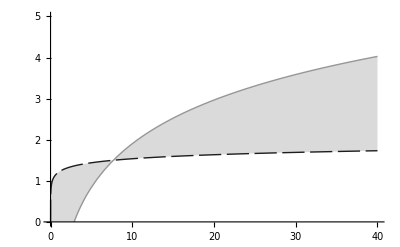

```mathematica
Plot[{SD2filled[x]*(DPS1QOE/maxQoE), HD2[x]},{x, 0, 40},PlotRange->{{0,40},{0,5}}, Filling->True, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}} ]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]
```

STAGE 2 (S2) TRANSFORMATIONS:

```mathematica
(* STAGE 2: BASE FORMULA *)
qclass[bw_] = 2.88537*Log[0.0078128*bw*1000]; (* map bandwidth/bitrate to quality classes as measured *)
HDCHGABW[bw_] = 3.01427+0.31634 * Log[qclass[bw]]; (* HD QoE curve under price cognitions s.t. bandwidth *)
HDCHGA[x_] = 3.01427+0.31634 * Log[x]; (* 3.0133859+0.9579225* Log[x] *)
HDCHGB[x_] = (v +3.01427+ w*0.31634* Log[x]); (* Stub function for SD -> parameterization below *)

(* USE STAGE 1 DATA *)
(* The DP of stage 1 determines the x-value for DP in stage two, but the MOS Value will be different and has to be different! *)
xminSD = Solve[SD2filled[x] == 0,{x}] [[1]];
xminHD = Solve[HD2[x] == 0, {x}] [[1]];
Solve[HDCHGA[x] ==  0, {x}]; (* TODO: AVOID MANUAL TRANSFER *)
(* calculate now HD_S2 * (SD_S1 / SD_S2) *)
xminSDnew = 0.00007274307483642649 (0.001925661443332294 / 2.885861437939618);

(*xDP = 5.54314236139844 (* copyied from above!!!!!!!!!!! stage 1*)*)
"New S2 MOS Value:"
mosDP = HDCHGA[xDP] (* What is the MOS at the new (sic!) curve at xDP? *)
(* k+1 service curve bw minimum on x-axis *)
```

New S2 MOS Value:

{3.65927}

We create a DP of MOS = 4.5 for the service with the lower user preference. The next best service is put at the equivalent to MOS = 1.5 (unaltered curve) on the new curve (mosDP resulting from the position of xDP of stage 1).

```mathematica
(*Solve[{HDCHGB[xDP] == maxQoE}, {w}]*)
Solve[{HDCHGB[xDP] == maxQoE}, {v}]
```

{{v→1.48573-0.644995 w}}

Let’s now consider the minimum point of the new curve. Contrary to the case where we have to distinct curves, we have to take care now that x-axis is shifted but uses the identical span -> the curve becomes flatter.

```mathematica
Solve[HDCHGB[x] == 0, {v}] /. x -> xminSDnew (*xminSD*)
(*{{w-> .5504 (1.4857300000000002-v)}}  /.%*)
```

{{v→-3.01427+5.32745 w}}

Solve the equation system, by setting the equations for v and w equal in order to derive w and v.

```mathematica
Solve[-3.01427+5.327445895723278 w== 1.4857300000000002-0.6449953079357288 w, w]
v -> -3.01427+5.327445895723278 w /.%
```

{{w→0.753461}}

{v→0.999751}

Now put it together ...  and verify if it has worked out.

```mathematica
"SD Curve S2:"
HDCHGB[x] /.{{{v->0.9997513546292298}}};
HDCHGBfilled[x_] = % /. {{w->0.7534607452046714}}
HDCHGBfilled[x_] = Flatten[HDCHGBfilled[x]][[1]]
```

SD Curve S2:

{{{4.01402+0.23835 Log[x]}}}

4.01402+0.23835 Log[x]

Sanity checks:

```mathematica
"Expected result: True (2)"
(*{{{{4.5} ==4.01402135462923+0.23834977213804576 Log[x]}}} /. x -> xDP*)
HDCHGBfilled[x] == {{{{4.5}}}} /. x -> xDP
HDCHGBfilled[x] == {{{0.}}} /. x -> xminSDnew
"Show minimum of new SD curve S2:"
HDCHGA[x] /. xminSD
```

Expected result: True (2)

{4.5}=={{{{4.5}}}}

0.=={{{0.}}}

Show minimum of new SD curve S2:

0.286957

And print + plot it ...

```mathematica
"Print the curves:"
"HD:" HDCHGA[x]
"SD:" HDCHGBfilled[x]
```

Print the curves:

HD: (3.01427+0.31634 Log[x])

SD: (4.01402+0.23835 Log[x])

```mathematica
((4.01402135462923+0.23834977213804576 Log[x])*(mosDP/maxQoE)- minQoE)/spanQoE
(HDCHGA[x]-minQoE)/spanQoE
```

{0.285714 (-1.+0.81317 (4.01402+0.23835 Log[x]))}

0.285714 (2.01427+0.31634 Log[x])

```mathematica
0.2857142857142857 (2.01427+0.31634 Log[x])
```

0.285714 (2.01427+0.31634 Log[x])

4.18121

{0.285714 (-1.+0.81317 (4.01402+0.23835 Log[x]))}

0.285714 (2.01427+0.31634 Log[x])

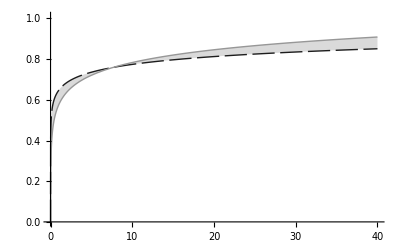

Use your fantasy to label axes or check the papers.

```mathematica
(* improved normalisation below *)
tempMaxQOE = HDCHGA[40] (* Maximum reached by the higher curve *)
HDCHGBfilledScaled[x_] = Flatten[((HDCHGBfilled[x])*(mosDP/maxQoE)- minQoE)/spanQoE]
HDCHGAScaled[x_] = ( HDCHGA[x]-minQoE)/spanQoE
Plot[{HDCHGBfilledScaled[x],HDCHGAScaled[x]},{x, 0, 40},PlotRange->{{0,40},{0,1.01}}, Filling->True, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}} ]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]
"Use your fantasy to label axes or check the papers."
```

```mathematica
(* Derive data points for simulation analysis (external) *) 
"HD:"
(*HDCHGA[40]
HDCHGA[x]/HDCHGA[40] /. x-> Range[0, 40, 1]*)
HDCHGAScaled[x] /. x-> Range[0, 40, 1]
"SD:"
HDCHGBfilledScaled[x]  /. x-> Range[0, 40, 1]
```

HD:

{-∞,0.575506,0.638154,0.674801,0.700803,0.720971,0.73745,0.751383,0.763452,0.774097,0.78362,0.792234,0.800099,0.807333,0.814031,0.820267,0.8261,0.83158,0.836746,0.841633,0.846269,0.850678,0.854883,0.858901,0.862747,0.866437,0.869982,0.873393,0.87668,0.879852,0.882916,0.885879,0.888749,0.89153,0.894228,0.896848,0.899394,0.901871,0.904281,0.906629,0.908917}

SD:

{{-∞,0.646881,0.685265,0.707718,0.723649,0.736006,0.746103,0.754639,0.762033,0.768556,0.77439,0.779668,0.784487,0.788919,0.793023,0.796844,0.800418,0.803775,0.80694,0.809934,0.812775,0.815477,0.818053,0.820514,0.822871,0.825132,0.827304,0.829394,0.831407,0.833351,0.835228,0.837044,0.838802,0.840506,0.842159,0.843764,0.845324,0.846842,0.848319,0.849757,0.851159}}

```mathematica
(* Improved normalisation *)
((4.01402135462923+0.23834977213804576 Log[x])*(mosDP/maxQoE)- minQoE)/spanQoE /. x-> Range[0, 40, 1]
( HDCHGA[x]-minQoE)/spanQoE /. x-> Range[0, 40, 1]
```

{{-∞,0.646881,0.685265,0.707718,0.723649,0.736006,0.746103,0.754639,0.762033,0.768556,0.77439,0.779668,0.784487,0.788919,0.793023,0.796844,0.800418,0.803775,0.80694,0.809934,0.812775,0.815477,0.818053,0.820514,0.822871,0.825132,0.827304,0.829394,0.831407,0.833351,0.835228,0.837044,0.838802,0.840506,0.842159,0.843764,0.845324,0.846842,0.848319,0.849757,0.851159}}

{-∞,0.575506,0.638154,0.674801,0.700803,0.720971,0.73745,0.751383,0.763452,0.774097,0.78362,0.792234,0.800099,0.807333,0.814031,0.820267,0.8261,0.83158,0.836746,0.841633,0.846269,0.850678,0.854883,0.858901,0.862747,0.866437,0.869982,0.873393,0.87668,0.879852,0.882916,0.885879,0.888749,0.89153,0.894228,0.896848,0.899394,0.901871,0.904281,0.906629,0.908917}

It worked out...
STAGE 3 TRANSFORMATIONS:

PARAMETERS (empirical input)

```mathematica
(* FROM THE QOMEX PAPER / FOR THE QOMEX PAPER *)
(* We have to perspective on WTP data. 
1) Global view (single-choice) following a beta distribution
	2) Local view (multi-choice; customer segments) rather following a normal distribution / gauss curve
*)

(* Stage 2 result curve -- UPDATE MANUALLY!!!!! TODO: Automate *)
(*lowerQoE[x_] =(3.39341129203281+0.5427299510110898 Log[x])*(1/3);*)
lowerQoE[x_] = (4.01402135462923+0.23834977213804576 Log[x]) * (mosDP/maxQoE);
xDP = 7.682389304300278;

(* Helpers to transition between quality classes and Mbits*)
(*qclass[bw_] =Round[ 2.88537*Log[0.0078128*bw]];*)
qclass[bw_] = 2.88537*Log[0.0078128*bw*1000];
r[x_] = Round[90.506*Exp[0.346576*(x+1)]]/1000; (* Mbits from classes *)



(* WTP curve in quality classes .. only for cross-checking or other purposes *)
wtpAorg[x_] = (Exp[-1.32512+-0.03140 * (qclass[x]+1)]) / (1+ Exp[-1.32512+-0.03140 * (qclass[x]+1)]);

(* WTP curves in Mbit/s! *)
wtpA[x_] = (Exp[-1.32512+-0.03140 * (qclass[x]+1)]) / (1+ Exp[-1.32512+-0.03140 * (qclass[x]+1)]);
wtpB[x_] = (Exp[-1.10596-0.07594 * (qclass[x]+1)]) / (1+ Exp[-1.10596+-0.07594 * (qclass[x]+1)]);
wtpC[x_] = (Exp[-1.00800-0.08073 * (qclass[x]+1)])/(1+Exp[-1.00800+-0.08073 * (qclass[x]+1)]);

(* Add customer segments curves *)
(* TODO: Currently manualled entered below *)
```

PRICES + REVENUE

Calculate factors to shift the revenues -> Static demand; altered price curve :

New SD price curve:

0.698836+0.000435308 x

(Known) HD price curve (repition):

0.0306373 (-0.128+3 x)

Price plot

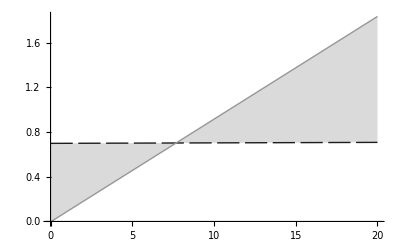

Revenue plot

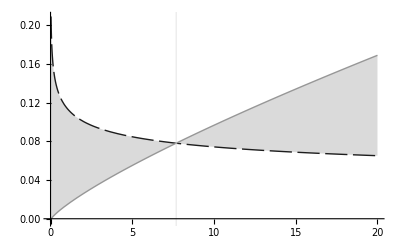

Use your fantasy to label axes or check the papers.

```mathematica
"Calculate factors to shift the revenues -> Static demand; altered price curve :"

(* PROCESS EXPLAINED:
Assume the demand can be kept static, then the price has to be equal at the DP for both services in order to satisfy the indifference by the user.

On the other hand, there is a preference of k over k+1, which is reflected in ASPW3. This factor fully hits when the quality difference is the biggest (at the maximum of the considered range, e.g. MOS = 4.0). Around these points a price curve can be constructed that keep the demand static ( a less trivial form). The outcome is the revenue as demand times price.

*)

(*Caculate ASPW*)
(*maxQoE = 4.0;*)
(*minQoE = 1.0;*)
maxBW = Solve[HDCHGA[x] == maxQoE, {x}] [[1]]; (* suprisingly high result, but OK *)
maxBWpar = x /. maxBW;

Solve[lowerQoE[x]== minQoE, x][[1]];
minQoEx = x /. % ;

(*ASPW3 = EuclideanDistance[{minQoEx,minQoE},{xDP,mnp}] / EuclideanDistance[{minQoEx, minQoE},{maxBWpar, maxQoE}] /. mnp -> xDP *)
(* ASPW Corrected after W12 *)
ASPW3 = EuclideanDistance[{minQoEx,minQoE},{xDP,mnp}] / EuclideanDistance[{minQoEx, minQoE},{maxBWpar, maxQoE}] /. mnp -> mosDP;

pmaxB = 3;
plow[x_] = k * x +d;
phigh[x_] = (pmaxB*x-0.128)/(32.768-0.128);

"New SD price curve:"
Solve[{plow[maxBWpar] == phigh[maxBWpar] *(ASPW3), plow[xDP]== phigh[xDP]}, {k,d}][[1]];
plow[x_] = plow[x] /. % 
"(Known) HD price curve (repition):"
phigh[x] 

(* Plot resulting curves *)

"Price plot"
(* price only *)
Plot[{plow[x], phigh[x]},{x,0,20},Filling-> {1 -> {2}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}] /.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"] 

"Revenue plot"
(* revenue estimate *)
Plot[{(plow[x]*wtpB [x]),(phigh[x]*wtpB [x])},{x, 0, 20}, GridLines->{{xDP},{}}, Filling-> {1 -> {2}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}] /.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"] (*PlotLegend->{"sine","cosine"}*)

"Use your fantasy to label axes or check the papers."
```

Local View: Show how the curves look like in different versions

Core plots:

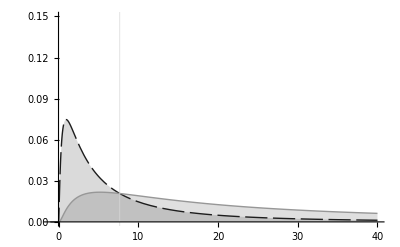

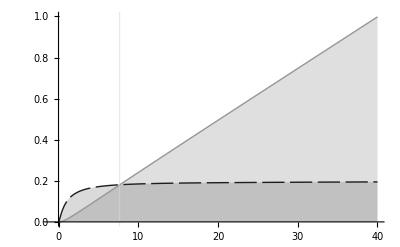

Use your fantasy to label axes or check the papers.

```mathematica
(* DATA PERSPECTIVE *)
(* LOCAL VIEW*)
"Local View: Show how the curves look like in different versions"
(* commented out for now – reactivate to inspect some interesting details *)
(*Plot[{Evaluate@Table[PDF[NormalDistribution[μ,σ],x],{μ,{6.839}},{σ,{3.234}}],Evaluate@Table[PDF[NormalDistribution[μ,σ],x],{μ,{5.824}},{σ,{3.735}}],Evaluate@Table[PDF[NormalDistribution[μ,σ],x],{μ,{5.086}},{σ,{3.524}}]},{x,-1,20}, PlotRange->{{-1,20},{0,0.15}},Filling->Axis]
Plot[{Evaluate@Table[PDF[NormalDistribution[μ,σ],qclass[x]],{μ,{6.839}},{σ,{3.234}}],Evaluate@Table[PDF[NormalDistribution[μ,σ],qclass[x]],{μ,{5.824}},{σ,{3.735}}],Evaluate@Table[PDF[NormalDistribution[μ,σ],qclass[x]],{μ,{5.086}},{σ,{3.524}}]},{x,-1,40}, PlotRange->{{-1,40},{0,0.15}},Filling->Axis]*)

"Core plots:"
(* customer segments *)
Plot[{plow[x]*Evaluate@Table[PDF[NormalDistribution[μ,σ],qclass[x]],{μ,{5.824}},{σ,{3.735}}],
phigh[x]*Evaluate@Table[PDF[NormalDistribution[μ,σ],qclass[x]],{μ,{5.824}},{σ,{3.735}}]
},{x,-1,40}, PlotRange->{{-1,40},{0,0.15}},Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"] 

(* the perspective to normalize for utility / USE IN THESIS!*)
(* currently manually normalised by using the maximum 3.71 *)
(* bwrange is used with phigh[bwrange] in order to normalize the plot in [0,1] *)
(* ToDo -> normalize the function instead in the future *)
bwrange = 40;

Plot[{plow[x]*Evaluate@Table[CDF[NormalDistribution[μ,σ],qclass[x]]/phigh[bwrange],{μ,{5.824}},{σ,{3.735}}],
phigh[x]*Evaluate@Table[CDF[NormalDistribution[μ,σ],qclass[x]] / phigh[bwrange],{μ,{5.824}},{σ,{3.735}}]
},{x,-1,40},PlotRange->{{-1,40},{0,1}},Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"] 

"Use your fantasy to label axes or check the papers."
```

LOCAL ISP UTILITY

Local ISP Utility

Local Utility gain of HD over SD (method I):

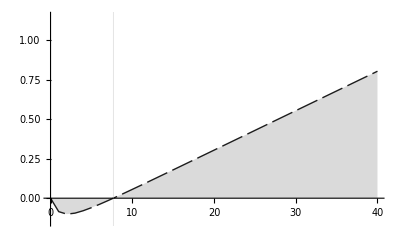

Local Utility gain of HD over SD (method II WRONG ADD that ... / phigh[bwrange]):

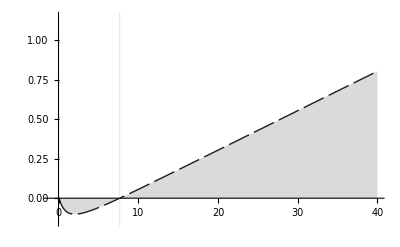

```mathematica
"Local ISP Utility"
(* Commented out to clean up – Rerun to see some interesting details *)
(*wtpA[128]
(Exp[-1.32512+-0.03140 * (0+1)]) / (1+ Exp[-1.32512+-0.03140 * (0+1)]) *)

localDemand = Evaluate@Table[CDF[NormalDistribution[μ,σ],qclass[x]],{μ,{5.824}},{σ,{3.735}}];
(*/. x-> Range[0,40,1];*)
localISPutilityLow = plow[x]*localDemand / phigh[bwrange] /. x-> Range[0,40,1];
localISPutilityHigh= phigh[x]*localDemand  / phigh[bwrange]/. x-> Range[0,40,1];

(*localISPutilityHigh[1][[2]]*)

(* Replace inderminate values – flatten first and replace value at position 1 with 0 *)
localISPutilityHigh = ReplacePart[Flatten[localISPutilityHigh], 1-> 0];
localISPutilityLow = ReplacePart[Flatten[localISPutilityLow], 1-> 0];
localispgaindata = Transpose@{Range[0,40],localISPutilityHigh - localISPutilityLow};



(*localispgaindata[[1]]
localispgaindata//.{x_List}:>temp*)
"Local Utility gain of HD over SD (method I):"
ListLinePlot[localispgaindata,PlotRange->{{0,40},{-0.15,1.15}}, Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]  /.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"] /.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"] 

"Local Utility gain of HD over SD (method II WRONG ADD that ... / phigh[bwrange]):"
(*Evaluate@Table[CDF[NormalDistribution[μ,σ],qclass[x]],{μ,{5.824}},{σ,{3.735}}] /. x -> 60 *)
Plot[{(phigh[x] - plow[x])*Evaluate@Table[CDF[NormalDistribution[μ,σ],qclass[x]],{μ,{5.824}},{σ,{3.735}}]/ phigh[bwrange]},{x,-1,40}, PlotRange->{{-1,40},{-0.15,1.15}},Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]
```

GLOBAL ISP UTILITY

```mathematica
(* GLOBAL VIEW *)
"Global ISP Utility: WARNING EXECUTION TAKES SOME TIME DUE TO LIVE INTEGRATION"
(* Basis for distribution function *)
WTPCDFunscaled[i_] := Integrate[(wtpB [x]),{x,0,i}]; (* demand is wtb / pmaxB *)

(* Map the integrated function to each value – general solution did not work *)
WTPCDFresultTemp = Map[WTPCDFunscaled,Range[0,40,1]]; (* in Mbit/s *)
(* normalize to make it classical CDF *)
WTPCDFresult = (WTPCDFresultTemp/Max[WTPCDFresultTemp]); (*Max[WTPCDFresult] *)
WTPCDFresult
(* Create functional form too. Do  not use a division by phigh[maxRange] due to rounding issues, but rather the maximum that is actually obtained *)
WTPCDF[i_] := WTPCDFunscaled[i]/  Max[WTPCDFresultTemp] (*Max[WTPCDFunscaled[Range[0,rangeMax]]];*)
"Consistent?"
WTPCDF[40] == 1

plowlist = plow[x] /. x -> Range[0,40,1];
phighlist = phigh[x] /. x -> Range[0,40,1];

(* link results together *)
(* division through phigh due to normalisation in 1 *)
"ISP UTILITY"
"Low (SD):"
globalISPutilityLow = plowlist * WTPCDFresult / phigh[bwrange] 
"High (HD):"
globalISPutilityHigh= phighlist * WTPCDFresult / phigh[bwrange]
```

Global ISP Utility: WARNING EXECUTION TAKES SOME TIME DUE TO LIVE INTEGRATION

{0.,0.0496577,0.0878716,0.122505,0.154972,0.185905,0.215661,0.244467,0.272482,0.29982,0.32657,0.3528,0.378565,0.40391,0.428873,0.453487,0.477778,0.501769,0.525483,0.548936,0.572145,0.595124,0.617887,0.640444,0.662806,0.684982,0.706982,0.728814,0.750484,0.772,0.793368,0.814593,0.835681,0.856637,0.877467,0.898173,0.918761,0.939234,0.959596,0.97985,1.}

Consistent?

True

ISP UTILITY

Low (SD):

{0.,0.00947531,0.0167774,0.0234046,0.0296259,0.0355614,0.0412788,0.0468216,0.0522195,0.0574944,0.0626628,0.0677377,0.0727295,0.0776468,0.0824966,0.0872851,0.0920172,0.0966975,0.10133,0.105918,0.110464,0.114971,0.119442,0.123878,0.128282,0.132656,0.137001,0.141318,0.145609,0.149875,0.154117,0.158337,0.162536,0.166713,0.170871,0.17501,0.179131,0.183234,0.18732,0.19139,0.195445}

High (HD):

{0.,0.00108601,0.00412559,0.00882411,0.0150495,0.0227159,0.0317606,0.0421343,0.0537966,0.0667136,0.0808562,0.0961988,0.112719,0.130395,0.149211,0.169148,0.190191,0.212326,0.235539,0.259819,0.285154,0.311533,0.338945,0.367381,0.396832,0.427289,0.458744,0.491189,0.524616,0.559018,0.594389,0.630721,0.668008,0.706245,0.745424,0.785541,0.82659,0.868565,0.911462,0.955275,1.}

1.

ISP Utility (global):

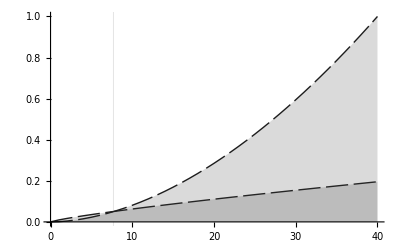

ISP Utility gain of HD over SD (global):

{0.,-0.0083893,-0.0126518,-0.0145805,-0.0145764,-0.0128454,-0.0095182,-0.00468732,0.00157708,0.00921927,0.0181935,0.0284612,0.0399892,0.0527487,0.0667141,0.0818626,0.0981736,0.115628,0.13421,0.153902,0.174691,0.196562,0.219503,0.243503,0.26855,0.294633,0.321744,0.349871,0.379008,0.409144,0.440272,0.472384,0.505473,0.539531,0.574553,0.610531,0.647459,0.685331,0.724142,0.763885,0.804555}

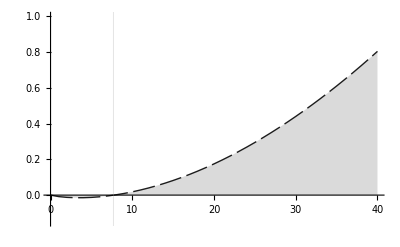

```mathematica
(* try to specify the utility gain or loss from ACTIVE degradations *)

"ISP Utility (global):"
ispdatalow =Transpose@{Range[0,40],globalISPutilityLow};
ispdatahigh= Transpose@{Range[0,40],globalISPutilityHigh};

p1 = ListLinePlot[ispdatalow, PlotRange->{{0,40},{0,1}},Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"];
p2 = ListLinePlot[ispdatahigh, PlotRange->{{0,40},{0,1}},Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"];

Show[p1,p2] (* combine the curves *)

"ISP Utility gain of HD over SD (global):"

ispgain = globalISPutilityHigh - globalISPutilityLow
ispdatagain =Transpose@{Range[0,40],ispgain};

p3 = ListLinePlot[ispdatagain,PlotRange->{{0,40},{-0.15,1}}, Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]  /.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]
```

STAGE 3 / Q-POINT DATA (!!!!!):

Keep in mind that the utility data partly comes from above.

```mathematica
(* ------------------------------------------------------------------------------------------
STEP1: RESCALE PL FIGURES
Step one rescale to fit the same data perspective *)
(* The maximum of the other curve is used rather than the considered maxMOS. Reason: We know that QoE is not affected by PL, if it is 0%, which was the test condition of the other test too.. what a coincidence ;) 
------------------------------------------------------------------------------------------
*)
```

```mathematica
Solve[ HDCHGA[x] == maxQoE, x ]
"Too high; unrealistically flat, let's go down to the max within a reasonable range"

(* Maximum value tested in the empirical data, see Globecom 13 publication. *)
rangeMax =  32.758; (* 40 *)
(* check whether scaling is correct.. is 40 range max? probably not.. shorten range *)
plQOETemp[x_] =HDCHGA[rangeMax]-(0.63*x); (* not user utility, but linearised QOE .. 4.7 *) (* 4.7 ;; HDCHGA[rangeMax];;*)
minPL = Solve[plQOETemp[x] == minQoE, x];
maxPL = Solve[plQOETemp[x] == HDCHGA[rangeMax], x] ;(* just cross-checking *)

(* Find an equation that matches the scale of the empirical WTP curve *)
(* Re-rescale results again for interpretation purposes *)
rescaleFactor = rangeMax/(x-0) /. minPL ; (* NOTE: x used instead of more concrete formulation in order to allow a replacement. Done identically for solving minPL and maxPL. Do not change. *)
pplneg[bwa_] = (rangeMax-bwa) / rescaleFactor;
plQoE[bw_] = plQOETemp[pplneg[bw]]  (* (rangeMax-x) / rescaleFactor *)




"Input data rescaling consistent:"
plQoE[0] == {minQoE} (* cross-checking correctness; spot for a "False" => otherwise all good *)

"Used MOS point:"
usedMOS = HDCHGA[rangeMax] - (HDCHGA[rangeMax] - minQoE)/2 (* Let's take the average instead *)

(* At which x is this input information now at the DP MOS defined above *)
usedXpl = Solve[plQoE[x] == usedMOS, x];
usedXhigh = Solve[HDCHGA[x] == usedMOS, x];


usedXplpar = x /. usedXpl; (* x-axis value for usedMOS *)
usedXhighpar = x /.usedXhigh; 

(* ------------------------------------------------------------------------------------------
STEP 2: Calculate prices (via ASPW etc.)

*)

(* ------------------------------------------------------------------------------------------
ARGUMENTATION:
NOW LET'S do a theoretic assessment
------------------------------------------------------
*)
(* Let's assume there was a theoretic reference curve (totally flat)and ASPWhigh is used to alternate from the point to reach our measured WTP result. In a similar sense, we can calculate the value for the PL metric.


By defining
(Known "high" price * ASPW_high) = Theory 
where "Theory" is an absolutely flat theoretic ref. curve (i.e., constant pricing; full demand retrieved)

and in anology defining
(Unknown PL price * ASPW_PL) = Theory


It becomes clear that the theoretic value "Theory" stays at 1 (by design of course), which is the maximum price. This means that the pricing would have been static to obtain the demand output as measured before, but it wasn't. 

So, originating from Measured WTP, we can derive the theoretic value
Theory = Measured High WTP / ASPW_high

Thus, we can derive the unknwon curve via
Theory / ASPW_PL = Unknown PL price
=> (Measured high price * ASPW_high) / ASPW_PL = Unknown PL price
=> Measured high price * ASPW_high / ASPW_PL = Unknown PL price
=> Unknown PL price = Measured high price * ASPW_high / ASPW_PL

As we know, the WTP figures were measured under 0% PL, from which we can infer that the quality range maximum is always identical (i.e., the maximum is fixed, while the other extremum needs parameterization)

Contrary to the ASPW from the QoMEX paper,the defined mid-point will be used as reference point for scaling (see the ASPW and euclidean distance parts below).

ASPW_high / ASPW_PL: Distance from minimum to used MOS relative to the considered range (So connecting a line from the range minimum to the max)

NOTE 1: Theoretical optimal is probably understood as something like an opt_quality curve for a metric where the curve stays statically at the best utility obtainable (the entire demand is retrieved that would be theoretically obtainable) without dropping at any point. So, the maximum price is used for the entire time => static price curve.
NOTE 2: The matching of the different quality metrics is undertaken at a "synchronization point" comparable to the "Switching Point" (SP) in the QoMEX paper, a point of comparison is defined where the difference is specified. Under no impairments the pricing has to be equal (second point). Between those two points a new linear curve can be built.
	
------------------------------------------------------------------------------------------
*)

(* probably 24 is usedXplpar *)

ASPWPL = EuclideanDistance[{minQoEx,minQoE},{usedXplpar[[1]],usedMOS}]/EuclideanDistance[{minQoEx, minQoE},{rangeMax, HDCHGA[rangeMax]}]; (* REMOVE MANUAL INPUT 24... 24.00841014340527 *)

ASPWhigh = EuclideanDistance[{minQoEx,minQoE},{usedXhighpar[[1]],usedMOS}] / EuclideanDistance[{minQoEx, minQoE},{rangeMax, HDCHGA[rangeMax]}]; (*/.  usedXhigh  ;*)

"WTPFactor"
WTPFactor = ASPWhigh / ASPWPL (* PL is higher as steeper *)

(* DEFINE BASE FUNCTIONS FOR INSERTION *)
pmaxB = 3;
ppl[x_] = k * x +d; (* Price function to be manipulated to keep demand static *)
phigh[x_] =  pmaxB *((x-0.128)/(32.768-0.128)); (* Measured HD video quality *)

(* ------------------------------------------------------------------------------------------
PARAM INSERTION: *)
(* Set the Price to keep the demand (WTP results) static
For that purpose, we set the maximum with 0% PL equal to the measured results and create a difference around the usedMOS point *)

(* ------------------------------------------------------------------------------------------
USE THE SAME POINT AS BEFORE *)
(* Remember: Measured high price * ASPW_high / ASPW_PL
Therefore: We orginate from the given high price curve point and derive the corresponding new price:
Solve[{ppl[usedXhighpar] == phigh[usedXhighpar] * scaleFactorTemp, ppl[rangeMax]== phigh[rangeMax]}, {k,d}][[1]]
ppl[x_] = ppl[x] /. % 

That leads to identical price curves again, if we use (as above) twice usedXhighpar. This proves the inference chain above, but does not provide us with the value we need. What we need is

ppl[usedXhighpar] == phigh[usedXhighpar]

which does not need rescaling. It inherently provides this difference, which is reflected in the WTPFactor value (0.0846).
------------------------------------------------------------------------------------------
 *)
scaleFactorTemp = WTPFactor; (* not used, but if you want to try the prove above, use it *)
Solve[{ppl[usedXplpar] == phigh[usedXhighpar], ppl[rangeMax]== phigh[rangeMax]}, {k,d}][[1]];
ppl[x_] = ppl[x] /. % ;

"Price consistent?"
ppl[rangeMax] == phigh[rangeMax]

"PRICES"
"PL"
ppllist = ppl[x] /. x -> Range[0,rangeMax,1] (* create a list of values *)
"Bitrate HD video ('high')"
phighlist = phigh[x] /. x -> Range[0,rangeMax,1] (* create a list of values *)

(* ------------------------------------------------------------------------------------------
STEP 3: Calculate utilities
*)

(* Let's calculate the utility now (AS IN THE QOMEX Paper) *)
(* Use the WTPCD result as source, norm it against the phigh that has been used to obtain the data and multiply it with the other price to keep the demand static, but affect the utility result *)

(* USE FROM ABOVE THE WTP CDF results = TARIFF B! Consistent with other data! *)
(* WARNING: DATA FROM OTHER CELL USED! / phigh[bwrange] 
------------------------------------------------------------------------------------------
*)

"UTILITIES"
"PL"
 (*Transpose@{Range[0,40],ppllist * WTPCDFresult} (*/ phigh[bwrange]*)*)
globalISPutilityPl= ppllist * WTPCDFresult[[1;;33]] / phigh[bwrange]
"Bitrate HD video ('high')"
globalISPutilityHighShort= phighlist * WTPCDFresult[[1;;33]] / phigh[bwrange]  (* Redundant; identical to the separate QoMEX calculation, but better redundant, but safe *)
"Still consistent data?"
globalISPutilityHigh[[33]] == 
globalISPutilityHighShort[[33]]
```

{{x→109.577}}

Too high; unrealistically flat, let's go down to the max within a reasonable range

{4.11803-0.0951837 (32.758-bw)}

Input data rescaling consistent:

True

Used MOS point:

2.55901

WTPFactor

0.0958452

Price consistent?

True

PRICES

PL

{-2.97902,-2.79653,-2.61403,-2.43154,-2.24905,-2.06656,-1.88406,-1.70157,-1.51908,-1.33658,-1.15409,-0.971598,-0.789106,-0.606613,-0.42412,-0.241627,-0.0591342,0.123359,0.305851,0.488344,0.670837,0.85333,1.03582,1.21832,1.40081,1.5833,1.76579,1.94829,2.13078,2.31327,2.49577,2.67826,2.86075}

Bitrate HD video ('high')

{-0.0117647,0.0801471,0.172059,0.263971,0.355882,0.447794,0.539706,0.631618,0.723529,0.815441,0.907353,0.999265,1.09118,1.18309,1.275,1.36691,1.45882,1.55074,1.64265,1.73456,1.82647,1.91838,2.01029,2.10221,2.19412,2.28603,2.37794,2.46985,2.56176,2.65368,2.74559,2.8375,2.92941}

UTILITIES

PL

{0.,-0.0378937,-0.0626788,-0.0812825,-0.0951073,-0.104833,-0.110873,-0.113509,-0.112948,-0.10935,-0.102844,-0.0935354,-0.0815147,-0.0668586,-0.0496339,-0.0299,-0.00770949,0.0168902,0.0438561,0.0731491,0.104733,0.138575,0.174645,0.212913,0.253353,0.29594,0.340651,0.387463,0.436356,0.48731,0.540305,0.595325,0.652351}

Bitrate HD video ('high')

{0.,0.00108601,0.00412559,0.00882411,0.0150495,0.0227159,0.0317606,0.0421343,0.0537966,0.0667136,0.0808562,0.0961988,0.112719,0.130395,0.149211,0.169148,0.190191,0.212326,0.235539,0.259819,0.285154,0.311533,0.338945,0.367381,0.396832,0.427289,0.458744,0.491189,0.524616,0.559018,0.594389,0.630721,0.668008}

Still consistent data?

True

```mathematica
(* LAST STEP: CREATE INVERSE PPLOS Function fpl in order to calculate from the given bw range back to the used packet loss percentage. fpl yields % of packets. This function is only a helper function. `*)
"[0,32] Mbits are {...} % packet loss:"
Map[pplneg, Range[0,IntegerPart[rangeMax]]]
"(keep in mind 32.768 is 0% loss)"

(* Create inverse function to pplneg to create bw from pl *)
"Function tracing back to bw from pl:"
fbw[pl_] = bw /.  Solve[pplneg[bw] ==  pl, bw][[1]]
```

[0,32] Mbits are {...} % packet loss:

{{4.94925},{4.79816},{4.64708},{4.49599},{4.34491},{4.19382},{4.04274},{3.89165},{3.74057},{3.58948},{3.4384},{3.28731},{3.13623},{2.98514},{2.83406},{2.68297},{2.53189},{2.3808},{2.22972},{2.07863},{1.92754},{1.77646},{1.62537},{1.47429},{1.3232},{1.17212},{1.02103},{0.869949},{0.718863},{0.567778},{0.416693},{0.265608},{0.114523}}

(keep in mind 32.768 is 0% loss)

Function tracing back to bw from pl:

-6.61878 (-4.94925+1. pl)

LINEARIZATION WORKS

line:

0.+0.0105827 x

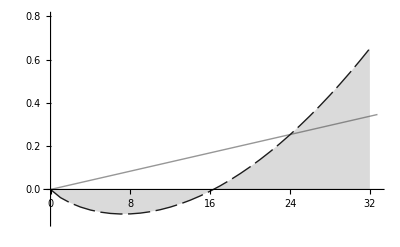

Now in PL dimension:

0.-0.0700448 (-4.94925+1. pl)

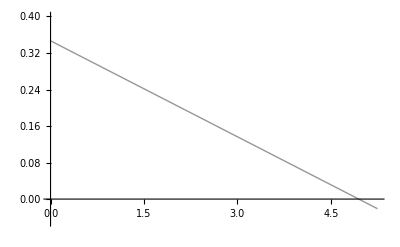

2.01029

Rescale to match the max:

2.01029 (0.-0.0700448 (-4.94925+1. pl))

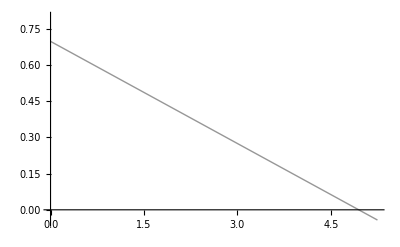

Rescale to match the max + revert to bw perspective:

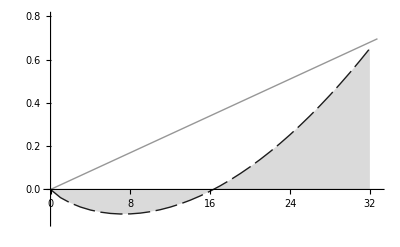

```mathematica
(* Linearization *)
(* Save the utility function *)
f[x_] = (ppl[x]  * WTPCDF[x])/phigh[bwrange]; (* max input param should be bwrange *)

(* Create data tuples for the considered range*)
datay= f[x] /. x -> Range[0,rangeMax,1];
datalinear= Transpose@{Range[0,32],datay};
"line:"
line=Fit[datalinear,{0,x},x]
pOrg= ListLinePlot[datalinear, PlotRange->{{0,rangeMax},{-0.15,0.8}},Filling->Axis, GridLines->{{xDP},{}}, PlotStyle->{{Blue,Dashing[{0.04,0.01}]},{Thick,Orange},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"];

pFit= Plot[line, {x,0,rangeMax}, PlotRange->{{0,rangeMax},{-0.15,0.8}}, PlotStyle->{{Thick,Orange},{Blue,Dashing[{0.04,0.01}]},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]; 

Show[pFit, pOrg] 

"Now in PL dimension:"
linepl = line /. x ->fbw[pl]
pFitpl= Plot[linepl, {pl,0,5.25}, PlotRange->{{0,5.25},{-0.05,0.4}}, PlotStyle->{{Thick,Orange},{Blue,Dashing[{0.04,0.01}]},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]
(* combine the curves *)

rescaleplline =f[x]/line /.x -> rangeMax

"Rescale to match the max:"
linepl * rescaleplline
pFitpl = Plot[linepl * rescaleplline, {pl,0,5.25}, PlotRange->{{0,5.25},{-0.05,0.8}}, PlotStyle->{{Thick,Orange},{Blue,Dashing[{0.04,0.01}]},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]

"Rescale to match the max + revert to bw perspective:"
pFitRescaled= Plot[line*rescaleplline, {x,0,rangeMax}, PlotRange->{{0,rangeMax},{-0.15,0.8}}, PlotStyle->{{Thick,Orange},{Blue,Dashing[{0.04,0.01}]},{Darker@Green,Thick}}]/.x:_RGBColor|_Hue|_CMYKColor:>ColorConvert[x,"Grayscale"]; 
Show[pFitRescaled, pOrg]
```

HELPERS

```mathematica
(* This is just some helper stuff for printing purposes. Replace test by an idea to round set to round it for the paper *)
test = {-∞,0.5755057142857142,0.6381543368852379,0.6748014318277913,0.7008029594847617,0.7209713112055437,0.737450054427315,0.7513826333006164,0.7634515820842853,0.7740971493698684,0.7836199338050674,0.7922343401705817,0.8000986770268388,0.8073331656398235,0.8140312559001401,0.8202670287476208,0.8261002046838092,0.8315796312167837,0.8367457719693921,0.8416325219055747,0.8462685564045912,0.8506783508426935,0.8548829627701056,0.8589006400762933,0.8627472996263625,0.8664369081253731,0.8699817882393472,0.8733928669119454,0.8766798784996639,0.8798515322451201,0.8829156513471446,0.8858792892190945,0.8887488272833328,0.8915300577126588,0.8942282538163076,0.8968482302204459,0.8993943945689158,0.901870792138821,0.9042811445050983,0.9066288831819006,0.908917179004115};
ReplaceAll[test,n_Real->Round[n,.001]]
```

```mathematica
pplneg[0]
```

{4.94925}